```mathematica
SetDirectory[NotebookDirectory[]];
```

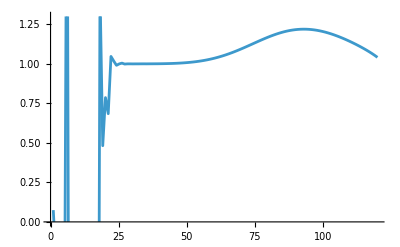

```mathematica
T=Flatten[Import["./T.dat"]];
chi2=Flatten[Import["./chi2.dat"]];
chi4=Flatten[Import["./chi4.dat"]];
r42=chi4/chi2;
ListLinePlot[Transpose[{T,r42}],PlotRange->{All,{0,1.3}}]
```